```mathematica
Guy F. Mongelli                                                            ChE 418
Prof. Teitel                                                                     2/21/2011
```

```mathematica
x=Ene/Nϵ
```

Ene/Nϵ

```mathematica
(-((1+x)/2)Log[(1+x)/2]-((1-x)/2)Log[(1-x)/2])/Nϵ
```

(-1/2 (1-Ene/Nϵ) Log[1/2 (1-Ene/Nϵ)]+1/2 (-1-Ene/Nϵ) Log[1/2 (1+Ene/Nϵ)])/Nϵ

```mathematica
((1+x)/2)/Nϵ
```

(1+Ene/Nϵ)/(2 Nϵ)

```mathematica
Clear[x]
```

```mathematica
S1[x_]=-((1+x)/2)Log[(1+x)/2]-((1-x)/2)Log[(1-x)/2]
```

-1/2 (1-x) Log[(1-x)/2]+1/2 (-1-x) Log[(1+x)/2]

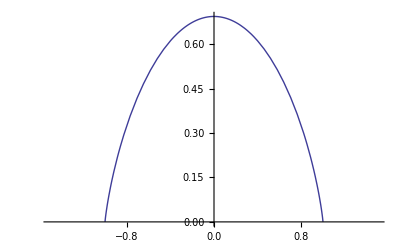

```mathematica
Plot[S1[x],{x,-1.5,1.5}]
```

```mathematica
N[S1[0],2]
```

0.69

```mathematica
T[x_]=1/Log[(1-x)/(1+x)]
```

1/Log[(1-x)/(1+x)]

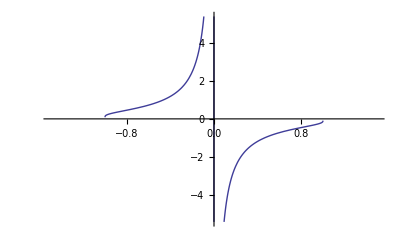

```mathematica
Plot[T[x],{x,-1.5,1.5}]
```

```mathematica
Guy Mongelli                                                                      ChE 418
Prof. Teitel                                                                      2/20/2011
```

```mathematica
Problem #1
```

```mathematica
Clear[Q1,QN,β]
```

```mathematica
β=1/(kb*T)
```

1/(kb T)

```mathematica
We know that this is the partition function for a single up and down spin system :
```

```mathematica
Q1[T_]=Exp[ϵ*β]+Exp[-ϵ*β]
```

ⅇ^(-β ϵ)+ⅇ^(β ϵ)

```mathematica
For N particles :
```

```mathematica
QN[V_,T_]=(Q1[T])^N
```

(ⅇ^(-β ϵ)+ⅇ^(β ϵ))^N

```mathematica
The Helmholtz free energy is :
```

```mathematica
A[N_,V_,T_]=kb*T*Log[QN[V,T]]
```

kb T Log[(ⅇ^(-β ϵ)+ⅇ^(β ϵ))^N]

```mathematica
The Entropy is :
```

```mathematica
S[V_,T_]=-D[A[N,V,T],T]
```

-(kb N T ((ⅇ^(-ϵ/(kb T)) ϵ)/(kb T^2)-(ⅇ^(ϵ/(kb T)) ϵ)/(kb T^2)))/(ⅇ^(-ϵ/(kb T))+ⅇ^(ϵ/(kb T)))-kb Log[(ⅇ^(-ϵ/(kb T))+ⅇ^(ϵ/(kb T)))^N]

```mathematica
Clear[Q1,QN,β]
```

```mathematica
Part B : We know that we need to eventually write the entropy as
```

```mathematica
S/n*kb=-1/2(1-x)Log[(1-x)/2]-1/2(1-x)Log[(1+x)/2]
```

```mathematica
To get there from here we notice that the result from the last assignment was entropy in terms of x, which was basically a change of variables from the energy function.  We have energy here but we need to eliminate temperature.  There is a relationship between energy and temperature that exists through the knowlege of the partition function.
```

```mathematica
Reevaluate the simgle particle partition
```

```mathematica
Q1[T_]=Exp[ϵ*β]+Exp[-ϵ*β]
```

ⅇ^(-β ϵ)+ⅇ^(β ϵ)

```mathematica
Consider N particles
```

```mathematica
QN[V_,T_]=(Q1[T])^N
```

(ⅇ^(-β ϵ)+ⅇ^(β ϵ))^N

```mathematica
The energy is given by (see lecture notes) :
```

```mathematica
Energy[V_,T_]=-D[Log[QN[V,T]],β]
```

-(N (-ⅇ^(-β ϵ) ϵ+ⅇ^(β ϵ) ϵ))/(ⅇ^(-β ϵ)+ⅇ^(β ϵ))

```mathematica
We will need to use the same change of variables as in the previous assignment.  Namely:
```

```mathematica
y=Exp[β*T],
x=Energy[V,T]/(N ϵ)
```

```mathematica
β==1/(kb*T)
```

True

```mathematica
Solve[Energy2==-N*ϵ*((Exp[β*ϵ]-Exp[-β*ϵ])/(Exp[β*ϵ]+Exp[-β*ϵ])),T]
```

{{}}

```mathematica
Simplify[-Energy[V,T]/(N ϵ)]
```

(-1+ⅇ^(2 β ϵ))/(1+ⅇ^(2 β ϵ))

```mathematica
β=1/(kb*T)
```

1/(kb T)

```mathematica
Energy[V,T]
```

-(N (-ⅇ^(-ϵ/(kb T)) ϵ+ⅇ^(ϵ/(kb T)) ϵ))/(ⅇ^(-ϵ/(kb T))+ⅇ^(ϵ/(kb T)))

```mathematica
Eng=N*ϵ*((Exp[β*ϵ]-Exp[-β*ϵ])/(Exp[β*ϵ]+Exp[-β*ϵ]))
```

((-ⅇ^(-β ϵ)+ⅇ^(β ϵ)) N ϵ)/(ⅇ^(-β ϵ)+ⅇ^(β ϵ))

```mathematica
Solve[Energy[V,T]==Energy,T]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→ϵ/(kb Log[-(√(-Energy+N ϵ))/(√(Energy+N ϵ))])},{T→ϵ/(kb Log[(√(-Energy+N ϵ))/(√(Energy+N ϵ))])}}

```mathematica
Solve[Eng==1,T]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→ϵ/(kb Log[-(√(1+N ϵ))/(√(-1+N ϵ))])},{T→ϵ/(kb Log[(√(1+N ϵ))/(√(-1+N ϵ))])}}

```mathematica
D[Log[2Cosh[β*ϵ]],β]
```

ϵ Tanh[β ϵ]

```mathematica
This gives :
```

```mathematica
Solve[(y-1/y)/(y+1/y)==-x,y]
```

{{y→-(√(1-x))/(√(1+x))},{y→(√(1-x))/(√(1+x))}}

```mathematica
Therefore, we can write the elements of the derived entropy function as terms of x and y.  The we can write the system completely in terms of x so that it looks like the entropy function from the last assignment.
```

```mathematica
Clear[x,y]
```

```mathematica
Entropy[x_,y_]=N*kb*Log[y+1/y]+x*Log[y]
```

Set::write: Tag Entropy in Entropy[x_, y_] is Protected.

x Log[y]+kb N Log[1/y+y]

```mathematica
Entropy[x0,y0]
```

Entropy::targ: Argument y0 at position 1 should be a List, a SparseArray, or a String.

Entropy[x0,y0]

```mathematica
y=√((1-x)/(1+x))
```

√((1-x)/(1+x))

```mathematica
Entropy[x,(√(1-x))/(√(1+x))]
```

Entropy::targ: Argument √1 - x/√1 + x at position 1 should be a List, a SparseArray, or a String.

Entropy[x,(√(1-x))/(√(1+x))]

```mathematica
FullSimplify[-1/2(1-x)Log[1/2]-1/2(1+x)Log[1/2]]
```

Log[2]

```mathematica
Simplify[-1/2(1-x)Log[1/2]-1/2(1+x)Log[1/2]-1/2(1-x)Log[1-x]-1/2(1+x)Log[1+x]]
```

1/2 (Log[4]+(-1+x) Log[1-x]-(1+x) Log[1+x])

```mathematica
Desired result for S/N*kb
```

```mathematica
-1/2(1-x)Log[(1-x)/2]-1/2(1-x)Log[(1+x)/2]
```

```mathematica
Problem #2
```

```mathematica
Ω[En_,V_,N_]=(V/h^3*(2π*m*En)^(3/2))^N *1/(((3*N)/2-1)!N!)(Δ/En)
```

((2 π)^(3 N/2) (((En m)^(3/2) V)/h^3)^N Δ)/(En N! (-1+(3 N)/2)!)

```mathematica
Re[β]>0
```

Re[β]>0

```mathematica
QN[T_,V_]=Integrate[1/Δ*Exp[-β*En]*Ω[En,V,N],{En,0,∞},Assumptions->{Re[N]>0,Re[β]>0}]
```

((2 π)^(3 N/2) ((m^(3/2) V)/h^3)^N β^(-3 N/2))/Gamma[1+N]

```mathematica
Problem 3
```

```mathematica
∫Exp[-β*p*V] V^N ⅆV
```

-V^(1+N) (p V β)^(-1-N) Gamma[1+N,p V β]

```mathematica
∫Exp[-β*p*V] V^(N-1)ⅆV
```

-V^N (p V β)^-N Gamma[N,p V β]

```mathematica
Z[T_,p_,n_]=(((2π*m*kb*T)/h^2)^(3/2))/V0((kb*T)/P)^(N+1)
```

(2 √2 π^(3/2) ((kb m T)/h^2)^(3/2) ((kb T)/P)^(1+N))/V0

```mathematica
G[T_,p_,n_]=-kb*T*Log[Z[T,p,n]]
```

-kb T Log[(2 √2 π^(3/2) ((kb m T)/h^2)^(3/2) ((kb T)/P)^(1+N))/V0]

```mathematica
Gprime[T_,p_,n_]=D[G[T,p,n],T]
```

-(kb T ((kb T)/P)^(-1-N) ((2 √2 kb (1+N) π^(3/2) ((kb m T)/h^2)^(3/2) ((kb T)/P)^N)/(P V0)+(3 √2 kb m π^(3/2) √((kb m T)/h^2) ((kb T)/P)^(1+N))/(h^2 V0)) V0)/(2 √2 π^(3/2) ((kb m T)/h^2)^(3/2))-kb Log[(2 √2 π^(3/2) ((kb m T)/h^2)^(3/2) ((kb T)/P)^(1+N))/V0]

```mathematica
G2prime[T_,p_,n_]=D[Gprime[T,p,n],T]
```

-1/(2 √2 π^(3/2) ((kb m T)/h^2)^(3/2))kb T ((kb T)/P)^(-1-N) ((2 √2 kb^2 N (1+N) π^(3/2) ((kb m T)/h^2)^(3/2) ((kb T)/P)^(-1+N))/(P^2 V0)+(6 √2 kb^2 m (1+N) π^(3/2) √((kb m T)/h^2) ((kb T)/P)^N)/(h^2 P V0)+(3 kb^2 m^2 π^(3/2) ((kb T)/P)^(1+N))/(√2 h^4 √((kb m T)/h^2) V0)) V0-(kb^2 (-1-N) T ((kb T)/P)^(-2-N) ((2 √2 kb (1+N) π^(3/2) ((kb m T)/h^2)^(3/2) ((kb T)/P)^N)/(P V0)+(3 √2 kb m π^(3/2) √((kb m T)/h^2) ((kb T)/P)^(1+N))/(h^2 V0)) V0)/(2 √2 P π^(3/2) ((kb m T)/h^2)^(3/2))+(3 kb^2 m T ((kb T)/P)^(-1-N) ((2 √2 kb (1+N) π^(3/2) ((kb m T)/h^2)^(3/2) ((kb T)/P)^N)/(P V0)+(3 √2 kb m π^(3/2) √((kb m T)/h^2) ((kb T)/P)^(1+N))/(h^2 V0)) V0)/(4 √2 h^2 π^(3/2) ((kb m T)/h^2)^(5/2))-(kb ((kb T)/P)^(-1-N) ((2 √2 kb (1+N) π^(3/2) ((kb m T)/h^2)^(3/2) ((kb T)/P)^N)/(P V0)+(3 √2 kb m π^(3/2) √((kb m T)/h^2) ((kb T)/P)^(1+N))/(h^2 V0)) V0)/(√2 π^(3/2) ((kb m T)/h^2)^(3/2))

```mathematica
FullSimplify[G2prime[T,p,n]]
```

-(kb (5+2 N))/(2 T)

```mathematica
∫_0^∞ p^2 Exp[-β*c*p]ⅆp
```

If[Re[c β]>0,2/(c^3 β^3),Integrate[ⅇ^(-c p β) p^2,{p,0,∞},Assumptions→Re[c β]≤0]]

```mathematica
QN=(((4π*V)/(h^3 c^3 β^2))^N)/(N!)
```

((4 π)^N (V/(c^3 h^3 β^2))^N)/(N!)

```mathematica
CLear[A[T]]
```

CLear[(-kb T Log[((4 π)^N (V/(c^3 h^3 β^2))^N)/(N!)])[T]]

```mathematica
A[T_]=-kb*T*Log[QN]
```

-kb T Log[((4 π)^N (V/(c^3 h^3 β^2))^N)/(N!)]

```mathematica
D[-A[T],V]
```

(kb N T)/V

```mathematica
En=-D[Log[QN],β]
```

(2 N)/β

```mathematica
Gibbs[T_]=A[T]+N*kb*T
```

kb N T-kb T Log[((4 π)^N (V/(c^3 h^3 β^2))^N)/(N!)]

```mathematica
Clear[V[T]]
```

Clear::ssym: V[T] is not a symbol or a string.

```mathematica
V[T_]=(N*kB*T)/p
```

(kB N T)/p

```mathematica
β[T]=1/(kb*T)
```

1/(kb T)

```mathematica
Gibbs[T_]=kb *N* T-kb* T Log[((4 π)^N (1/(c^3 h^3 β[T]^3))^N)/(N!)((N*kB*T)/p)^N]
```

kb N T-kb T Log[((4 π)^N ((kB N T)/p)^N ((kb^3 T^3)/(c^3 h^3))^N)/(N!)]

```mathematica
Entrop[T_]=-D[Gibbs[T],T]
```

-kb N+kb (4 π)^-N T ((kB N T)/p)^-N ((kb^3 T^3)/(c^3 h^3))^-N ((3 kb^3 N (4 π)^N T^2 ((kB N T)/p)^N ((kb^3 T^3)/(c^3 h^3))^(-1+N))/(c^3 h^3 N!)+(kB N^2 (4 π)^N ((kB N T)/p)^(-1+N) ((kb^3 T^3)/(c^3 h^3))^N)/(p N!)) N!+kb Log[((4 π)^N ((kB N T)/p)^N ((kb^3 T^3)/(c^3 h^3))^N)/(N!)]

```mathematica
FullSimplify[Entrop[T]]
```

kb (3 N+Log[((4 π)^N ((kB N T)/p)^N ((kb^3 T^3)/(c^3 h^3))^N)/(N!)])

```mathematica
Clear[Cp]
```

```mathematica
Cp[T_]=T*D[Entrop[T],T]
```

T (kb (4 π)^-N T ((kB N T)/p)^-N ((kb^3 T^3)/(c^3 h^3))^-N ((9 kb^6 (-1+N) N (4 π)^N T^4 ((kB N T)/p)^N ((kb^3 T^3)/(c^3 h^3))^(-2+N))/(c^6 h^6 N!)+(3 2^(1+2 N) kb^3 kB N^3 π^N T^2 ((kB N T)/p)^(-1+N) ((kb^3 T^3)/(c^3 h^3))^(-1+N))/(c^3 h^3 p N!)+(3 2^(1+2 N) kb^3 N π^N T ((kB N T)/p)^N ((kb^3 T^3)/(c^3 h^3))^(-1+N))/(c^3 h^3 N!)+(kB^2 (-1+N) N^3 (4 π)^N ((kB N T)/p)^(-2+N) ((kb^3 T^3)/(c^3 h^3))^N)/(p^2 N!)) N!-1/(c^3 h^3)3 kb^4 N (4 π)^-N T^3 ((kB N T)/p)^-N ((kb^3 T^3)/(c^3 h^3))^(-1-N) ((3 kb^3 N (4 π)^N T^2 ((kB N T)/p)^N ((kb^3 T^3)/(c^3 h^3))^(-1+N))/(c^3 h^3 N!)+(kB N^2 (4 π)^N ((kB N T)/p)^(-1+N) ((kb^3 T^3)/(c^3 h^3))^N)/(p N!)) N!-1/p kb kB N^2 (4 π)^-N T ((kB N T)/p)^(-1-N) ((kb^3 T^3)/(c^3 h^3))^-N ((3 kb^3 N (4 π)^N T^2 ((kB N T)/p)^N ((kb^3 T^3)/(c^3 h^3))^(-1+N))/(c^3 h^3 N!)+(kB N^2 (4 π)^N ((kB N T)/p)^(-1+N) ((kb^3 T^3)/(c^3 h^3))^N)/(p N!)) N!+2^(1-2 N) kb π^-N ((kB N T)/p)^-N ((kb^3 T^3)/(c^3 h^3))^-N ((3 kb^3 N (4 π)^N T^2 ((kB N T)/p)^N ((kb^3 T^3)/(c^3 h^3))^(-1+N))/(c^3 h^3 N!)+(kB N^2 (4 π)^N ((kB N T)/p)^(-1+N) ((kb^3 T^3)/(c^3 h^3))^N)/(p N!)) N!)

```mathematica
FullSimplify[Cp[T]]
```

4 kb N

```mathematica
Guy Mongelli                                                                                   ChE 418
Prof. Teitel                                                                                   4/25/2011
```

```mathematica
Assignment #6
```

```mathematica
Problem #1
```

```mathematica
Part A :
```

```mathematica
f[v_,z_]=1/Gamma[v]∫_0^∞ x^(v-1)/(z^-1 Exp[x]+1)ⅆx
```

1/Gamma[v]z If[Re[v]>0,-(Gamma[v] PolyLog[v,-z])/z,Integrate[x^(-1+v)/(ⅇ^x+z),{x,0,∞},Assumptions→Re[v]≤0]]

```mathematica
f[5/2,-z]
```

-PolyLog[5/2,z]

```mathematica
-PolyLog[5/2,z]
```

-PolyLog[5/2,z]

```mathematica
The function that we have derived multiple times in class and Mathematica' s PolyLog unction are equivalent.
```

```mathematica
Series[PolyLog[5/2,z],{z,0,4}]
```

z+z^2/(4 √2)+z^3/(9 √3)+z^4/32+O[z]^5

```mathematica
The above function allows us to expand the Polylog function as a series, as wsa done in lecture.
```

```mathematica
2^(5/2)
```

4 √2

```mathematica
The fermi energy was given as :
```

```mathematica
EF=FullSimplify[((3 N)/(4π*g *V))^(2/3)( h^2/(2m))];
```

```mathematica
The density of states in this ideal, non - relativistic case is :
```

```mathematica
g[ϵ_]=(8*g*V*π*m)/h^3 ϵ^(3/2)
```

(8 g m π V ϵ^(3/2))/h^3

```mathematica
The integral of the density of states from zero energy to the fermi level will dictate the fermi energy.
```

```mathematica
mewnaught=Simplify[∫_0^ef g[ϵ]ⅆϵ]
```

(16 ef^(5/2) g m π V)/(5 h^3)

```mathematica
If we solve for the chemical potential as a function of temperature from the implicit definition arrived at in lecture 21.  This has the same dependance on the density of states and the fermi energy.  However, these two quantities have new values based upon the fact that the system is non - relativistic and ideal
```

```mathematica
Solve[μ==mewnaught+(μ-ef)g[ϵ]ef+π^2/6(k*T)^2(g[ef]-ef*g'[ef]),μ]
```

{{μ→(2 (-24 ef^(5/2) g m π V+5 ef^(3/2) g k^2 m π^3 T^2 V+60 ef^2 g m π V ϵ^(3/2)))/(15 (-h^3+8 ef g m π V ϵ^(3/2)))}}

```mathematica
ef=EF
```

(3^(2/3) h^2 (N/(g V))^(2/3))/(4 2^(1/3) m π^(2/3))

```mathematica
The following lines of code resolve the temperature dependence of the chemical potential but sustitute in for the value of the fermi energy
```

```mathematica
FullSimplify[Solve[μ==mewnaught+(μ-ef)g[ϵ]ef+π^2/6(k*T)^2(g[ef]-ef*g'[ef]),μ]]
```

{{μ→(h^2 N (N/(g V))^(1/3) ((5 2^(1/3) k^2 π^(8/3) T^2)/(√((h^2 (N/(g V))^(2/3))/m))-6 3^(2/3) √((h^2 (N/(g V))^(2/3))/m)+30 2^(1/6) (3 π)^(1/3) ϵ^(3/2)))/(20 2^(5/6) (-h m π^(2/3)+6^(2/3) g m π (N/(g V))^(2/3) V ϵ^(3/2)))}}

```mathematica
Clear[μ]
```

```mathematica
μ[T_]=(h^2 N (N/(g V))^(1/3) ((5 2^(1/3) k^2 π^(8/3) T^2)/(√((h^2 (N/(g V))^(2/3))/m))-6 3^(2/3) √((h^2 (N/(g V))^(2/3))/m)+30 2^(1/6) (3 π)^(1/3) ϵ^(3/2)))/(20 2^(5/6) (-h m π^(2/3)+6^(2/3) g m π (N/(g V))^(2/3) V ϵ^(3/2)));
```

```mathematica
Clear[Entropy]
```

Clear::wrsym: Symbol Entropy is Protected.

```mathematica
Part B :
```

```mathematica
Here we use the for expanded form of the chemical potential at low temperature derived in Part A and take the derivative as expressed in the question statement :
```

```mathematica
Entropy[T_]=FullSimplify[D[-N*μ[T],T]]
```

(g k^2 m N π^2 T ((h^2 (N/(g V))^(2/3))/m)^(3/2) V)/(2 √2 h^2 (h-6^(2/3) g π^(1/3) (N/(g V))^(2/3) V ϵ^(3/2)))

```mathematica
The limit of the chemical potential as the temperature goes to zero
```

```mathematica
FullSimplify[Limit[μ[T],T->0]]
```

(3 3^(1/3) h^2 N (N/(g V))^(1/3) (-3^(1/3) √((h^2 (N/(g V))^(2/3))/m)+5 2^(1/6) π^(1/3) ϵ^(3/2)))/(10 2^(5/6) (-h m π^(2/3)+6^(2/3) g m π (N/(g V))^(2/3) V ϵ^(3/2)))

```mathematica
mewnaught
```

(3 g m (3/π)^(2/3) ((h^2 (N/(g V))^(2/3))/m)^(5/2) V)/(10 2^(5/6) h^3)

```mathematica
This is the limit of the Entropy function as temperature goes to zero and agrees with the third law of thermodynamics.
```

```mathematica
Limit[(g k^2 m N π^2 T ((h^2 (N/(g V))^(2/3))/m)^(3/2) V)/(2 √2 h^2 (h-6^(2/3) g π^(1/3) (N/(g V))^(2/3) V ϵ^(3/2))),T->0]
```

0

```mathematica
The entropy function on p. 201 of pathria is frist order in T and therefore goes to zero as the temperature goes to zero.  This is expected in order to agree with the third law of thermodynamics.  These derivations are equivalent.  As we have seen many times, it is possiblt to obtain equivalent expressions for the fundamental thermodynamics variables by using different free energy formulations since they all step from the partition function.
```

```mathematica
Problem #2
```

```mathematica
To approach this problem we will observe inequalities in the number density of zero spin bosons as derived in lecture 23.  When there is an inequality, a Bose-Einstein Condensate will form.  We must alter the derivation in lecture in two ways.  First, the density of  states will change (the number of states with a certain energy will depend on the dimensionality).  Also, the
```

```mathematica
The ratio N/V will be denoted m:
```

```mathematica
ϵ[p_,s_]=A*Abs[p]^s
```

A Abs[p]^s

```mathematica
In 1 D space, N[k] will be given as :
```

```mathematica
N1[k_]=(k*L)/π
```

(k L)/π

```mathematica
Also, in 2 & 3 D space :
```

```mathematica
N2[k_]=(k^2L^2)/(4*π)
```

(k^2 L^2)/(4 π)

```mathematica
N3[k_]=(4π*k^3*L^3)/(3*8*π^3)
```

(k^3 L^3)/(6 π^2)

```mathematica
Now, finding the number of wavevectors per unit ' volume' :
```

```mathematica
G1[k_]=N1[k]/L
```

k/π

```mathematica
G2[k_]=N2[k]/L^2
```

k^2/(4 π)

```mathematica
G3[k_]=N3[k]/L^3
```

k^3/(6 π^2)

```mathematica
Define the wavevector/energy relationship :
```

```mathematica
Clear[k]
```

```mathematica
k[En_]=√((2*m*En)/h^2)
```

√2 √((En m)/h^2)

```mathematica
The following lines of code rewrite the energy functions as function of energy instead of wavevector
```

```mathematica
H1[En_]=G1[k[En]]
```

(√2 √((En m)/h^2))/π

```mathematica
H2[En_]=G2[k[En]]
```

(En m)/(2 h^2 π)

```mathematica
H3[En_]=G3[k[En]]
```

(√2 ((En m)/h^2)^(3/2))/(3 π^2)

```mathematica
To get the density of states, we must take the derivative of the number of states per unit volume with respect to energy :
```

```mathematica
Expand[D[H1[En],En]]
```

(√((En m)/h^2))/(√2 En π)

```mathematica
The 1 D case goes as one over the square root of energy as expected
```

```mathematica
FullSimplify[D[H2[En],En]]
```

m/(2 h^2 π)

```mathematica
The 2 D case does not vary with energy .
```

```mathematica
D[H3[En],En]
```

(m √((En m)/h^2))/(√2 h^2 π^2)

```mathematica
The 3 D case goes as the square root of energy as expected.
```

```mathematica
m[z_,s_]=Evaluate[∫_0^∞ p^(1/2)/(z^-1 Exp[-β*ϵ[p]])ⅆp,Assumptions->{s>0}]
```

Sequence[1/(8 π^3)z If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-3/(2 s)) Gamma[3/(2 s)])/s,Integrate[ⅇ^(A p^s β) √p,{p,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0}]

```mathematica
For the case of s = 1 :
```

```mathematica
m1[z_,s_]=Evaluate[∫_0^∞ G1[k]/(z^-1 Exp[-β*ϵ[k]])ⅆk,Assumptions->{s>0,A>0,Element[{A,s},Reals]}]
```

Sequence[1/π √2 √((En m)/h^2) z If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),(-A β)^(-1/s) Gamma[1+1/s],Integrate[ⅇ^(A k^s β),{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

```mathematica
m1[1,s]
```

Sequence[1/π √2 √((En m)/h^2) If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),(-A β)^(-1/s) Gamma[1+1/s],Integrate[ⅇ^(A k^s β),{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

```mathematica
m2[z_,s_]=Evaluate[∫_0^∞ G2[k]/(z^-1 Exp[-β*ϵ[k]])ⅆk,Assumptions->{s>0,A>0,Element[{A,s},Reals]}]
```

Sequence[1/(4 π)z If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-3/s) Gamma[3/s])/s,Integrate[ⅇ^(A k^s β) k^2,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

```mathematica
m2[1,s]
```

Sequence[1/(4 π)If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-3/s) Gamma[3/s])/s,Integrate[ⅇ^(A k^s β) k^2,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

```mathematica
m3[z_,s_]=Evaluate[∫_0^∞ G3[k]/(z^-1 Exp[-β*ϵ[k]])ⅆk,Assumptions->{s>0,A>0,Element[{A,s},Reals]}]
```

Sequence[1/(6 π^2)z If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-4/s) Gamma[4/s])/s,Integrate[ⅇ^(A k^s β) k^3,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

```mathematica
m3[1,s]
```

Sequence[1/(6 π^2)If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-4/s) Gamma[4/s])/s,Integrate[ⅇ^(A k^s β) k^3,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

```mathematica
FullSimplify[m[z,1]]
```

1/(8 π^3)z If[Re[A β]<0&&(A∉Reals||Re[A]≠0),(√π)/(2 (-A β)^(3/2)),Integrate[ⅇ^(A p β) √p,{p,0,∞},Assumptions→A==0||Re[A β]≥0]]

```mathematica
For the case of s = 2 :
```

```mathematica
FullSimplify[m[z,2]]
```

1/(8 π^3)z If[Re[A β]<0&&(A∉Reals||Re[A]≠0),Gamma[3/4]/(2 (-A β)^(3/4)),Integrate[ⅇ^(A p^2 β) √p,{p,0,∞},Assumptions→A==0||Re[A β]≥0]]

```mathematica
For the case of s = 3 :
```

```mathematica
FullSimplify[m[z,3]]
```

1/(8 π^3)z If[Re[A β]<0&&(A∉Reals||Re[A]≠0),(√π)/(3 √(-A β)),Integrate[ⅇ^(A p^3 β) √p,{p,0,∞},Assumptions→A==0||Re[A β]≥0]]

```mathematica
Part C:
```

```mathematica
f[v_,z_]=1/Gamma[v]∫_0^∞ x^(v-1)/(z^-1 Exp[x]+1)ⅆx
```

1/Gamma[v]z If[Re[v]>0,-(Gamma[v] PolyLog[v,-z])/z,Integrate[x^(-1+v)/(ⅇ^x+z),{x,0,∞},Assumptions→Re[v]≤0]]

```mathematica
f[5/2,z]
```

```mathematica
-PolyLog[5/2,z]
```

-PolyLog[5/2,z]

```mathematica
Series[PolyLog[5/2,z],{z,0,4}]
```

z+z^2/(4 √2)+z^3/(9 √3)+z^4/32+O[z]^5

```mathematica
2^(5/2)
```

4 √2

```mathematica
EF=FullSimplify[((3 N)/(4π*g *V))^(2/3)( h^2/(2m))];
```

```mathematica
g[ϵ_]=(8*g*V*π*m)/h^3 ϵ^(3/2)
```

(8 g m π V ϵ^(3/2))/h^3

```mathematica
mewnaught=Simplify[∫_0^ef g[ϵ]ⅆϵ]
```

(16 ef^(5/2) g m π V)/(5 h^3)

```mathematica
Solve[μ==mewnaught+(μ-ef)g[ϵ]ef+π^2/6(k*T)^2(g[ef]-ef*g'[ef]),μ]
```

{{μ→(2 (-24 ef^(5/2) g m π V+5 ef^(3/2) g k^2 m π^3 T^2 V+60 ef^2 g m π V ϵ^(3/2)))/(15 (-h^3+8 ef g m π V ϵ^(3/2)))}}

```mathematica
ef=EF
```

(3^(2/3) h^2 (N/(g V))^(2/3))/(4 2^(1/3) m π^(2/3))

```mathematica
FullSimplify[Solve[μ==mewnaught+(μ-ef)g[ϵ]ef+π^2/6(k*T)^2(g[ef]-ef*g'[ef]),μ]]
```

{{μ→(h^2 N (N/(g V))^(1/3) ((5 2^(1/3) k^2 π^(8/3) T^2)/(√((h^2 (N/(g V))^(2/3))/m))-6 3^(2/3) √((h^2 (N/(g V))^(2/3))/m)+30 2^(1/6) (3 π)^(1/3) ϵ^(3/2)))/(20 2^(5/6) (-h m π^(2/3)+6^(2/3) g m π (N/(g V))^(2/3) V ϵ^(3/2)))}}

```mathematica
Clear[μ]
```

```mathematica
μ[T_]=(h^2 N (N/(g V))^(1/3) ((5 2^(1/3) k^2 π^(8/3) T^2)/(√((h^2 (N/(g V))^(2/3))/m))-6 3^(2/3) √((h^2 (N/(g V))^(2/3))/m)+30 2^(1/6) (3 π)^(1/3) ϵ^(3/2)))/(20 2^(5/6) (-h m π^(2/3)+6^(2/3) g m π (N/(g V))^(2/3) V ϵ^(3/2)));
```

```mathematica
Clear[Entropy]
```

Clear::wrsym: Symbol Entropy is Protected.

```mathematica
Entropy[T_]=FullSimplify[D[-N*μ[T],T]]
```

Set::write: Tag Entropy in Entropy[T_] is Protected.

(g k^2 m N π^2 T ((h^2 (N/(g V))^(2/3))/m)^(3/2) V)/(2 √2 h^2 (h-6^(2/3) g π^(1/3) (N/(g V))^(2/3) V ϵ^(3/2)))

```mathematica
Limit[μ[T],T->0]
```

(3 h^2 N (N/(g V))^(1/3) (-3^(2/3) √((h^2 (N/(g V))^(2/3))/m)+5 2^(1/6) (3 π)^(1/3) ϵ^(3/2)))/(10 2^(5/6) m π^(2/3) (-h+6^(2/3) g π^(1/3) (N/(g V))^(2/3) V ϵ^(3/2)))

```mathematica
Limit[Entropy[T],T->0]
```

Entropy::targ: Argument T at position 1 should be a List, a SparseArray, or a String.

Limit[Entropy[T],T→0]

```mathematica
Guy Mongelli                                                                              ChE 418
Prof. Teitel                                                                             3/13/2011
```

```mathematica
Assignment #4
```

```mathematica
Problem 1
```

```mathematica
FullSimplify[∫_0^∞ Exp[-β*m*ω^2 1/2*Abs[r^2]]ⅆr]
```

Piecewise[{{(√(π/2))/(√(m β ω^2)), Re[m β ω^2]≥0}, {Integrate[ⅇ^(-1/2 m β ω^2 Abs[r]^2),{r,0,∞},Assumptions→Re[m β ω^2]<0], True}}]

```mathematica
Clear[QN]
```

```mathematica
QN[T_]=FullSimplify[1/(N!)(V/h^3(2π*m*k*T)^(3/2))^N((√(π/2))/(√(m ω^2 β)))^N]
```

(2^N π^(2 N) (((k m T)^(3/2) V)/h^3)^N (m β ω^2)^(-N/2))/(N!)

```mathematica
QN1[β_]=(2^N π^(2 N) ((( m β)^(3/2) V)/h^3)^N (m ω^2 β)^(-N/2))/(N!)
```

(2^N π^(2 N) ((V (m β)^(3/2))/h^3)^N (m β ω^2)^(-N/2))/(N!)

```mathematica
FullSimplify[-D[Log[QN1[β]],β]]
```

-N/β

```mathematica
Problem #3
```

```mathematica
Qideal[i_]=((1/(N!))[V/h^3(2π*m*k*T)^(3/2)])^N,
Q=∏_(i=1)^N Qideal[i_]
```

```mathematica
Guy Mongelli                                                                                   ChE 418
Prof. Teitel                                                                                   4/25/2011
```

```mathematica
Assignment #6
```

```mathematica
Problem #1
```

```mathematica
Part A :
```

```mathematica
f[v_,z_]=1/Gamma[v]∫_0^∞ x^(v-1)/(z^-1 Exp[x]+1)ⅆx
```

(z If[Re[v]>0,-(Gamma[v] PolyLog[v,-z])/z,Integrate[x^(-1+v)/(ⅇ^x+z),{x,0,∞},Assumptions→Re[v]≤0]])/Gamma[v]

```mathematica
f[5/2,-z]
```

-PolyLog[5/2,z]

```mathematica
-PolyLog[5/2,z]
```

-PolyLog[5/2,z]

```mathematica
The function that we have derived multiple times in class and Mathematica' s PolyLog unction are equivalent.
```

```mathematica
Series[PolyLog[5/2,z],{z,0,4}]
```

z+z^2/(4 √2)+z^3/(9 √3)+z^4/32+O[z]^5

```mathematica
The above function allows us to expand the Polylog function as a series, as was done in lecture.
```

```mathematica
2^(5/2)
```

4 √2

```mathematica
The fermi energy was given as :
```

```mathematica
EF=FullSimplify[((3 N)/(4π*g *V))^(2/3)( h^2/(2m))];
```

```mathematica
The density of states in this ideal, non - relativistic case is :
```

```mathematica
g[ϵ_]=(8*g*V*π*m)/h^3 ϵ^(3/2)
```

(8 g m π V ϵ^(3/2))/h^3

```mathematica
The integral of the density of states from zero energy to the fermi level will dictate the fermi energy.
```

```mathematica
mewnaught=Simplify[∫_0^ef g[ϵ]ⅆϵ]
```

(16 ef^(5/2) g m π V)/(5 h^3)

```mathematica
If we solve for the chemical potential as a function of temperature from the implicit definition arrived at in lecture 21.  This has the same dependance on the density of states and the fermi energy.  However, these two quantities have new values based upon the fact that the system is non - relativistic and ideal
```

```mathematica
Solve[μ==mewnaught+(μ-ef)g[ϵ]ef+π^2/6(k*T)^2(g[ef]-ef*g'[ef]),μ]
```

{{μ→(2 (-24 ef^(5/2) g m π V+5 ef^(3/2) g k^2 m π^3 T^2 V+60 ef^2 g m π V ϵ^(3/2)))/(15 (-h^3+8 ef g m π V ϵ^(3/2)))}}

```mathematica
ef=EF
```

(3^(2/3) h^2 (N/(g V))^(2/3))/(4 2^(1/3) m π^(2/3))

```mathematica
The following lines of code resolve the temperature dependence of the chemical potential but sustitute in for the value of the fermi energy
```

```mathematica
FullSimplify[Solve[μ==mewnaught+(μ-ef)g[ϵ]ef+π^2/6(k*T)^2(g[ef]-ef*g'[ef]),μ]]
```

{{μ→(h^2 N (N/(g V))^(1/3) ((5 2^(1/3) k^2 π^(8/3) T^2)/(√((h^2 (N/(g V))^(2/3))/m))-6 3^(2/3) √((h^2 (N/(g V))^(2/3))/m)+30 2^(1/6) (3 π)^(1/3) ϵ^(3/2)))/(20 2^(5/6) (-h m π^(2/3)+6^(2/3) g m π (N/(g V))^(2/3) V ϵ^(3/2)))}}

```mathematica
Clear[μ]
```

```mathematica
μ[T_]=(h^2 N (N/(g V))^(1/3) ((5 2^(1/3) k^2 π^(8/3) T^2)/(√((h^2 (N/(g V))^(2/3))/m))-6 3^(2/3) √((h^2 (N/(g V))^(2/3))/m)+30 2^(1/6) (3 π)^(1/3) ϵ^(3/2)))/(20 2^(5/6) (-h m π^(2/3)+6^(2/3) g m π (N/(g V))^(2/3) V ϵ^(3/2)));
```

```mathematica
Clear[Entropy]
```

Clear::wrsym: Symbol Entropy is Protected.

```mathematica
Part B :
```

```mathematica
Here we use the for expanded form of the chemical potential at low temperature derived in Part A and take the derivative as expressed in the question statement :
```

```mathematica
Entropy[T_]=FullSimplify[D[-N*μ[T],T]]
```

Set::write: Tag Entropy in Entropy[T_] is Protected.

(g k^2 m N π^2 T ((h^2 (N/(g V))^(2/3))/m)^(3/2) V)/(2 √2 h^2 (h-6^(2/3) g π^(1/3) (N/(g V))^(2/3) V ϵ^(3/2)))

```mathematica
The limit of the chemical potential as the temperature goes to zero
```

```mathematica
FullSimplify[Limit[μ[T],T->0]]
```

(3 3^(1/3) h^2 N (N/(g V))^(1/3) (-3^(1/3) √((h^2 (N/(g V))^(2/3))/m)+5 2^(1/6) π^(1/3) ϵ^(3/2)))/(10 2^(5/6) (-h m π^(2/3)+6^(2/3) g m π (N/(g V))^(2/3) V ϵ^(3/2)))

```mathematica
mewnaught
```

(3 g m (3/π)^(2/3) ((h^2 (N/(g V))^(2/3))/m)^(5/2) V)/(10 2^(5/6) h^3)

```mathematica
This is the limit of the Entropy function as temperature goes to zero and agrees with the third law of thermodynamics.
```

```mathematica
Limit[(g k^2 m N π^2 T ((h^2 (N/(g V))^(2/3))/m)^(3/2) V)/(2 √2 h^2 (h-6^(2/3) g π^(1/3) (N/(g V))^(2/3) V ϵ^(3/2))),T->0]
```

0

```mathematica
The entropy function on p. 201 of pathria is frist order in T and therefore goes to zero as the temperature goes to zero.  This is expected in order to agree with the third law of thermodynamics.  These derivations are equivalent.  As we have seen many times, it is possiblt to obtain equivalent expressions for the fundamental thermodynamics variables by using different free energy formulations since they all step from the partition function.
```

```mathematica
Problem #2
```

```mathematica
To approach this problem we will observe inequalities in the number density of zero spin bosons as derived in lecture 23.  When there is an inequality, a Bose-Einstein Condensate will form.  We must alter the derivation in lecture in two ways.  First, the density of  states will change (the number of states with a certain energy will depend on the dimensionality).  Also, the
```

```mathematica
The ratio N/V will be denoted m:
```

```mathematica
ϵ[p_,s_]=A*Abs[p]^s
```

A Abs[p]^s

```mathematica
In 1 D space, N[k] will be given as :
```

```mathematica
N1[k_]=(k*L)/π
```

(k L)/π

```mathematica
Also, in 2 & 3 D space :
```

```mathematica
N2[k_]=(k^2L^2)/(4*π)
```

(k^2 L^2)/(4 π)

```mathematica
N3[k_]=(4π*k^3*L^3)/(3*8*π^3)
```

(k^3 L^3)/(6 π^2)

```mathematica
Now, finding the number of wavevectors per unit ' volume' :
```

```mathematica
G1[k_]=N1[k]/L
```

k/π

```mathematica
G2[k_]=N2[k]/L^2
```

k^2/(4 π)

```mathematica
G3[k_]=N3[k]/L^3
```

k^3/(6 π^2)

```mathematica
Define the wavevector/energy relationship :
```

```mathematica
Clear[k]
```

```mathematica
k[En_]=√((2*m*En)/h^2)
```

√2 √((En m)/h^2)

```mathematica
The following lines of code rewrite the energy functions as function of energy instead of wavevector
```

```mathematica
H1[En_]=G1[k[En]]
```

(√2 √((En m)/h^2))/π

```mathematica
H2[En_]=G2[k[En]]
```

(En m)/(2 h^2 π)

```mathematica
H3[En_]=G3[k[En]]
```

(√2 ((En m)/h^2)^(3/2))/(3 π^2)

```mathematica
To get the density of states, we must take the derivative of the number of states per unit volume with respect to energy :
```

```mathematica
Expand[D[H1[En],En]]
```

(√((En m)/h^2))/(√2 En π)

```mathematica
The 1 D case goes as one over the square root of energy as expected
```

```mathematica
FullSimplify[D[H2[En],En]]
```

m/(2 h^2 π)

```mathematica
The 2 D case does not vary with energy .
```

```mathematica
D[H3[En],En]
```

(m √((En m)/h^2))/(√2 h^2 π^2)

```mathematica
The 3 D case goes as the square root of energy as expected.
```

```mathematica
m[z_,s_]=Evaluate[∫_0^∞ p^(1/2)/(z^-1 Exp[-β*ϵ[p,s]])ⅆp,Assumptions->{s>0}]
```

Sequence[z If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-3/(2 s)) Gamma[3/(2 s)])/s,Integrate[ⅇ^(A p^s β) √p,{p,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0}]

```mathematica
For the case of s = 1, we will use the densite of waves in space for the 1D case :
```

```mathematica
m1[z_,s_]=Evaluate[∫_0^∞ G1[k]/(z^-1 Exp[-β*ϵ[k,s]])ⅆk,Assumptions->{s>0,A>0,Element[{A,s},Reals]}]
```

Sequence[1/π z If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-2/s) Gamma[2/s])/s,Integrate[ⅇ^(A k^s β) k,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

```mathematica
m1[1,s]
```

Sequence[1/π If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-2/s) Gamma[2/s])/s,Integrate[ⅇ^(A k^s β) k,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

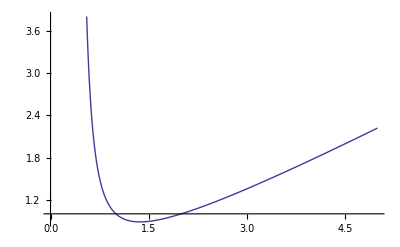

```mathematica
Plot[Gamma[2/s],{s,0,5}]
```

```mathematica
m1simple[s_]=1/(s*π)(-A*β)^(-2/s)Gamma[2/s]
```

((-A β)^(-2/s) Gamma[2/s])/(π s)

```mathematica
For the case of s=2, we must necessarily use the density of states per unit volume in 2D:
```

```mathematica
m2[z_,s_]=Evaluate[∫_0^∞ G2[k]/(z^-1 Exp[-β*ϵ[k,s]])ⅆk,Assumptions->{s>0,A>0,Element[{A,s},Reals]}]
```

Sequence[1/(4 π)z If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-3/s) Gamma[3/s])/s,Integrate[ⅇ^(A k^s β) k^2,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

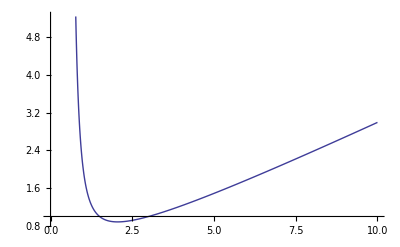

```mathematica
Plot[Gamma[3/s],{s,0,10}]
```

```mathematica
m2[1,s]
```

Sequence[1/(4 π)If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-3/s) Gamma[3/s])/s,Integrate[ⅇ^(A k^s β) k^2,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

```mathematica
Simmilarly for 3D:
```

```mathematica
m3[z_,s_]=Evaluate[∫_0^∞ G3[k]/(z^-1 Exp[-β*ϵ[k,s]])ⅆk,Assumptions->{s>0,A>0,Element[{A,s},Reals]}]
```

Sequence[1/(6 π^2)z If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-4/s) Gamma[4/s])/s,Integrate[ⅇ^(A k^s β) k^3,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

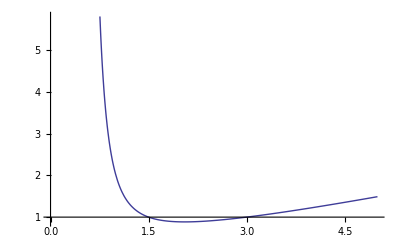

```mathematica
Plot[Gamma[3/s],{s,0,5}]
```

```mathematica
m3[1,s]
```

Sequence[1/(6 π^2)If[s>0&&Re[A β]<0&&(A∉Reals||Re[A]≠0),((-A β)^(-4/s) Gamma[4/s])/s,Integrate[ⅇ^(A k^s β) k^3,{k,0,∞},Assumptions→A==0||Re[A β]≥0||s≤0]],Assumptions→{s>0,A>0,(A|s)∈Reals}]

```mathematica
FullSimplify[m[z,1]]
```

z If[Re[A β]<0&&(A∉Reals||Re[A]≠0),(√π)/(2 (-A β)^(3/2)),Integrate[ⅇ^(A p β) √p,{p,0,∞},Assumptions→A==0||Re[A β]≥0]]

```mathematica
For the case of s = 2 :
```

```mathematica
FullSimplify[m[z,2]]
```

z If[Re[A β]<0&&(A∉Reals||Re[A]≠0),Gamma[3/4]/(2 (-A β)^(3/4)),Integrate[ⅇ^(A p^2 β) √p,{p,0,∞},Assumptions→A==0||Re[A β]≥0]]

```mathematica
For the case of s = 3 :
```

```mathematica
FullSimplify[m[z,3]]
```

z If[Re[A β]<0&&(A∉Reals||Re[A]≠0),(√π)/(3 √(-A β)),Integrate[ⅇ^(A p^3 β) √p,{p,0,∞},Assumptions→A==0||Re[A β]≥0]]

```mathematica
Manipulate[Plot[Zeta[x,a],{x,0,100}],{a,{1,2,3}}]
```

```mathematica
N [Zeta[3/2],3]
```

2.61

```mathematica
N[Zeta[5/2],3]
```

1.34

```mathematica
Zeta[1]
```

ComplexInfinity

```mathematica
N[Zeta[2],3]
```

1.64

```mathematica
N[Zeta[1/2],3]
```

-1.46

```mathematica
TableForm[Table[N[Zeta[s/d],3],{s,1,10},{d,1,5}],TableHeadings->{{"s=1","s=2","s=3","s=4","s=5","s=6","s=7","s=8","s=9","s=10"},{"d = 1","d = 2","d = 3","d = 4","d = 5"}}]
```

| d = 1 | d = 2 | d = 3 | d = 4 | d = 5
s=1 | ComplexInfinity | -1.46 | -0.973 | -0.813 | -0.734
s=2 | 1.64 | ComplexInfinity | -2.45 | -1.46 | -1.13
s=3 | 1.2 | 2.61 | ComplexInfinity | -3.44 | -1.95
s=4 | 1.08 | 1.64 | 3.6 | ComplexInfinity | -4.44
s=5 | 1.04 | 1.34 | 2.12 | 4.6 | ComplexInfinity
s=6 | 1.02 | 1.2 | 1.64 | 2.61 | 5.59
s=7 | 1.01 | 1.13 | 1.41 | 1.96 | 3.11
s=8 | 1. | 1.08 | 1.28 | 1.64 | 2.29
s=9 | 1. | 1.05 | 1.2 | 1.46 | 1.88
s=10 | 1. | 1.04 | 1.15 | 1.34 | 1.64

```mathematica
Problem #4
```

```mathematica
b=(Tanh[β(z/2)J*m+h])^2
```

Tanh[h+1/2 J m z β]^2

```mathematica
c=Tanh[β(z/2)J*m+h]
```

Tanh[h+1/2 J m z β]

```mathematica
a=D[Tanh[β(z/2)J*m+h],z]
```

1/2 J m β Sech[h+1/2 J m z β]^2

```mathematica
d[h_]=FullSimplify[(a-b)/c]
```

J m β Csch[2 h+J m z β]-Tanh[h+1/2 J m z β]

```mathematica
Limit[d[h],h->0]
```

J m β Csch[J m z β]-Tanh[1/2 J m z β]